## Elipse Para Corte

Abrindo Arquivos

```mathematica
string=NotebookDirectory[];
fileplace=string <>"Elipse1.png";
fileplace2=string <>"Elipse2.png";
FigElipse=Import[fileplace];
FigElipse2=Import[fileplace2];
```

Primeira Elipse

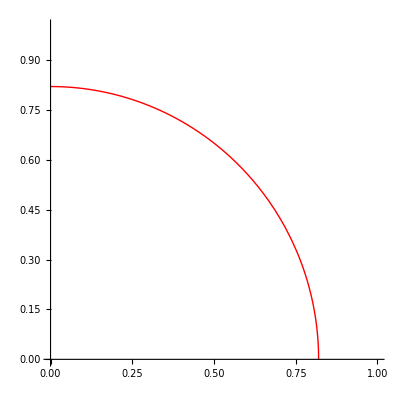

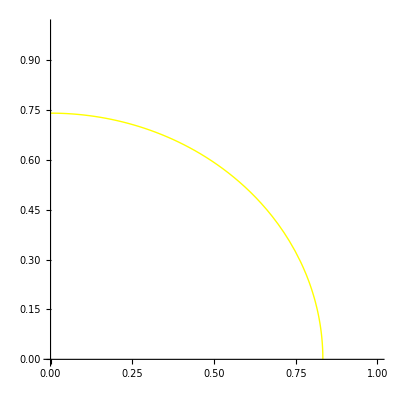

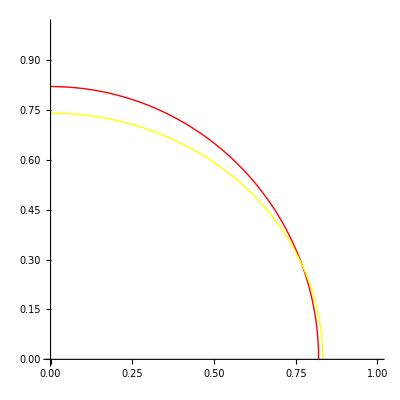

-Graphics-

1.01585

0.902439

```mathematica
r=0.82;
y=Sqrt[r^2-x^2];
circ=Plot[y,{x,0,r},PlotRange->{{0,1},{0,1}},AspectRatio->Automatic,PlotStyle->{Red,Thick}]
a=0.833;
b=0.74;
elipse=Plot[Sqrt[b^2(1-x^2/a^2)],{x,0,a},PlotRange->{{0,1},{0,1}},AspectRatio->Automatic,PlotStyle->{Yellow}]
pos=265;
dupla=Show[circ,elipse]
ImageCompose[FigElipse,dupla,{pos,pos}]
a/r//N
b/r//N
```

Segunda Elipse

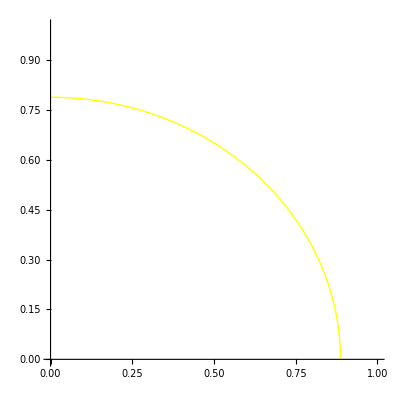

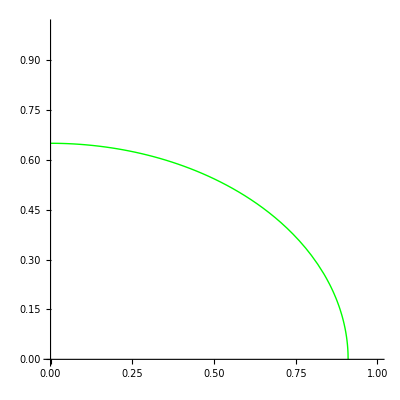

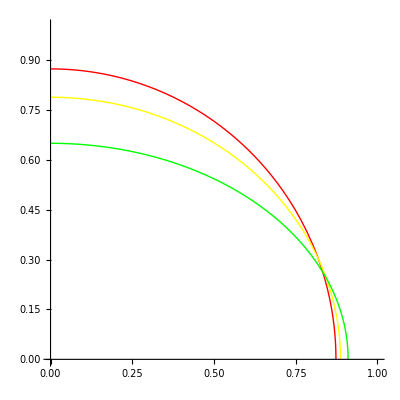

-Graphics-

1.01585

0.902439

1.04268

0.743902

```mathematica
r=0.873;
y=Sqrt[r^2-x^2];
circ=Plot[y,{x,0,r},PlotRange->{{0,1},{0,1}},AspectRatio->Automatic,PlotStyle->{Red,Thick}];
a=0.833 r/0.82;
b=0.74 r/0.82;
a1=0.855r/0.82;
b1=0.61r/0.82;
elipse=Plot[Sqrt[b^2(1-x^2/a^2)],{x,0,a},PlotRange->{{0,1},{0,1}},AspectRatio->Automatic,PlotStyle->{Yellow,Thick}]
elipse2=Plot[Sqrt[b1^2(1-x^2/a1^2)],{x,0,a1},PlotRange->{{0,1},{0,1}},AspectRatio->Automatic,PlotStyle->{Green,Thick}]
pos=265;
trio=Show[circ,elipse,elipse2]
ImageCompose[FigElipse2,trio,{pos,pos}]
a/r
b/r
a1/r
b1/r
```

Fatores de Escala

0.7744-x^2

0.5329 (1-1.20758 x^2)

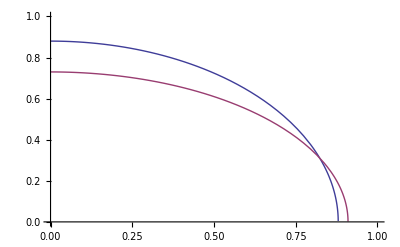

{{x→-0.823079},{x→0.823079}}

```mathematica
y1=(0.88^2-x^2)
y2=(1-x^2/a^2)b^2/.{a->0.91,b->0.73}
Plot[{Sqrt[y1],Sqrt[y2]},{x,0,1},PlotRange->{{0,1},{0,1}}]
Solve[y1==y2,x]
```

```mathematica
0.91/0.88
0.73/0.88
```

1.03409

0.829545

1-x^2

0.688146 (1-0.935153 x^2)

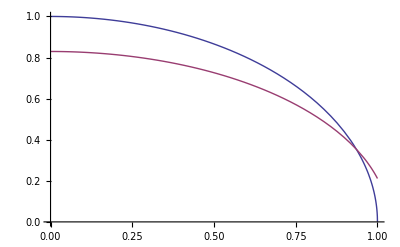

{{x→-0.935318},{x→0.935318}}

```mathematica
y1=(1-x^2)
y2=(1-x^2/a^2)b^2/.{a->0.91/0.88,b->0.73/0.88}
Plot[{Sqrt[y1],Sqrt[y2]},{x,0,1},PlotRange->{{0,1},{0,1}}]
Solve[y1==y2,x]
contour = 0.0003
```